## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOutRectangular.csv"],"CSV",HeaderLines->1];

αs=(Transpose@mydata)[[1]];
τs=(Transpose@mydata)[[2]];(*in IGeV*)
rs=(Transpose@mydata)[[3]];(*in IGeV*)
Dτs=(Transpose@mydata)[[4]];(*in IGeV*)
Drs=(Transpose@mydata)[[5]];(*in IGeV*)
urs=(Transpose@mydata)[[6]]; (*dimensionless*)
uτs=(Transpose@mydata)[[7]]; (*dimensionless*)
```

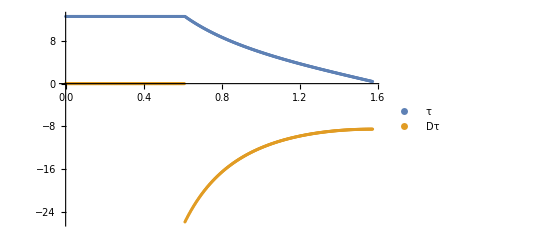

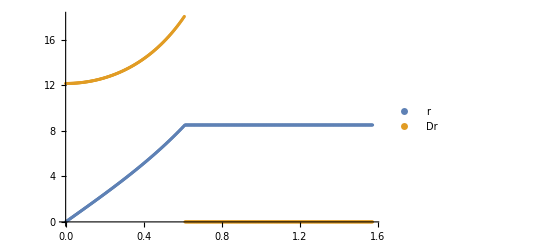

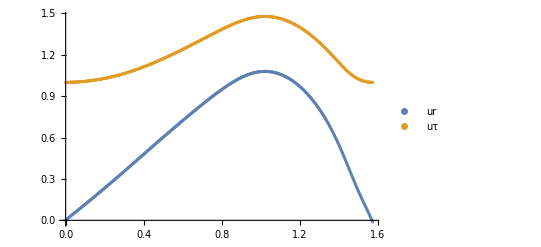

```mathematica
ListPlot[{Transpose@{αs,τs},Transpose@{αs,Dτs}},PlotLegends->{"τ","Dτ"}]
ListPlot[{Transpose@{αs,rs},Transpose@{αs,Drs}},PlotLegends->{"r","Dr"}]
ListPlot[{Transpose@{αs,urs},Transpose@{αs,uτs}},PlotLegends->{"ur","uτ"}]
```

### Define Interpolating Functions from the Data

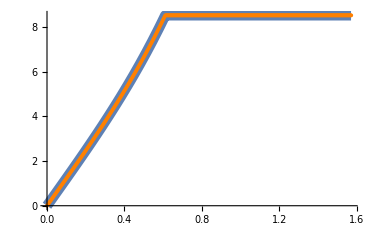

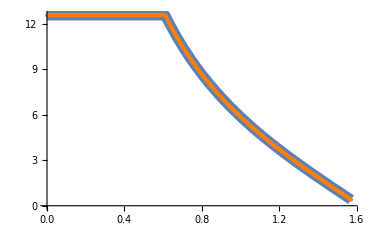

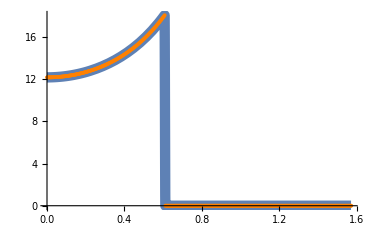

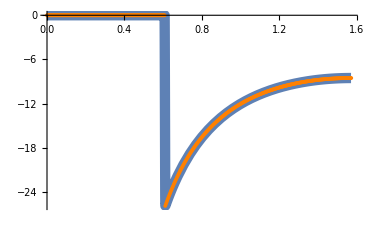

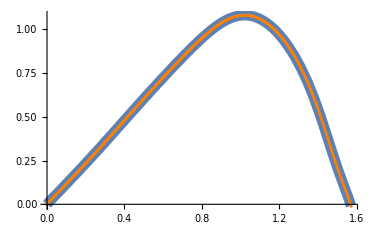

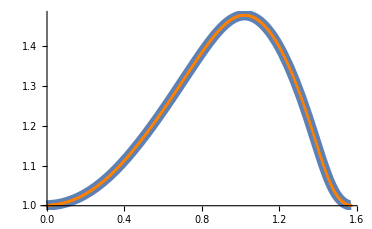

```mathematica
r=Interpolation[Transpose@{αs,rs}];
τ=Interpolation[Transpose@{αs,τs}];
Dr=Interpolation[Transpose@{αs,Drs},InterpolationOrder->1];
Dτ=Interpolation[Transpose@{αs,Dτs},InterpolationOrder->1];
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
Show[
Plot[r[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,rs},PlotStyle->{Orange}]
]
Show[
Plot[τ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,τs},PlotStyle->{Orange}]
]
Show[
Plot[Dr[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,Drs},PlotStyle->{Orange}]
]
Show[
Plot[Dτ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,Dτs},PlotStyle->{Orange}]
]
Show[
Plot[ur[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,urs},PlotStyle->{Orange}]
]
Show[
Plot[uτ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,uτs},PlotStyle->{Orange}]
]
```

### Define field data from a already calculated spectrum (c++ code) in order to double check validity of code...

```mathematica
parentdir=StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/spectra_real_m140_constfield_20241029_110519/"];
allspecs=FileNames[All,parentdir];
myspec=allspecs[[1]]
Short[myfieldscsv=Import[StringJoin[myspec,"/field0.txt"],"CSV"],5]
Short[myDfieldscsv=Import[StringJoin[myspec,"/field0_deriv.txt"],"CSV"],5]

myfields=myfieldscsv[[3;;]];
fieldsAlphas=(Transpose@myfields)[[1]];
fieldsRe=(Transpose@myfields)[[2]];
fieldsIm=(Transpose@myfields)[[3]];

myDfields=myDfieldscsv[[3;;]];
DfieldsAlphas=(Transpose@myDfields)[[1]];
DfieldsRe=(Transpose@myDfields)[[2]];
DfieldsIm=(Transpose@myDfields)[[3]];

fieldRe=Interpolation[Transpose@{fieldsAlphas,fieldsRe}];
fieldIm=Interpolation[Transpose@{fieldsAlphas,fieldsIm}];
DfieldRe=Interpolation[Transpose@{fieldsAlphas,DfieldsRe}];
DfieldIm=Interpolation[Transpose@{fieldsAlphas,DfieldsIm}];
```

/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/data/spectra_real_m140_constfield_20241029_110519/spec_20241029_112541

{{# 20241029_112541},{alpha,field0Re,field0Im},{0,0.127797,0},{0.00157237,0.127797,0},{0.00314474,0.127797,0},{0.00471711,0.127797,0},{0.00628947,0.127797,0},{0.00786184,0.127797,0},{0.00943421,0.127797,0},{0.0110066,0.127797,0},{0.0125789,0.127797,0},«981»,{1.55665,0.127797,0},{1.55822,0.127797,0},{1.55979,0.127797,0},{1.56136,0.127797,0},{1.56293,0.127797,0},{1.56451,0.127797,0},{1.56608,0.127797,0},{1.56765,0.127797,0},{1.56922,0.127797,0},{1.5708,0.127797,0}}

{{# 20241029_112541},{alpha,Dfield0Re,Dfield0Im},{0,0,0},{0.00157237,0,0},{0.00314474,0,0},{0.00471711,0,0},{0.00628947,0,0},{0.00786184,0,0},{0.00943421,0,0},{0.0110066,0,0},{0.0125789,0,0},{0.0141513,0,0},{0.0157237,0,0},{0.0172961,0,0},{0.0188684,0,0},«972»,{1.54878,0,0},{1.55036,0,0},{1.55193,0,0},{1.5535,0,0},{1.55507,0,0},{1.55665,0,0},{1.55822,0,0},{1.55979,0,0},{1.56136,0,0},{1.56293,0,0},{1.56451,0,0},{1.56608,0,0},{1.56765,0,0},{1.56922,0,0},{1.5708,0,0}}

### ...or define alternative field functions for other testing purposes

```mathematica
Clear[fieldRe,fieldIm,DfieldRe,DfieldIm]
fieldRe[x_]:=0.1278;
fieldIm[x_]:=0;
DfieldRe[x_]:=0;
DfieldIm[x_]:=0;
```

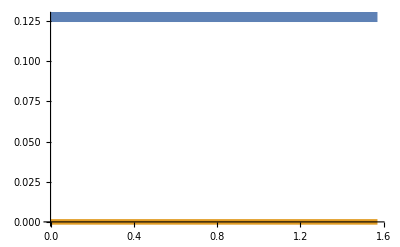

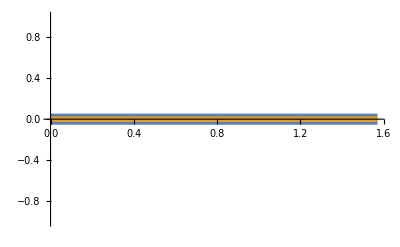

```mathematica
Plot[{fieldRe[x],fieldIm[x]},{x,0,Pi/2},PlotStyle->{{Thickness[0.02]},{Thickness[0.01]}}]
Plot[{DfieldRe[x],DfieldIm[x]},{x,0,Pi/2},PlotStyle->{{Thickness[0.02]},{Thickness[0.01]}}]
```

## Compute the Fourier Spectrum of the Source

```mathematica
mπ=0.14;
GeVtoIfm=5.0677;
fmtoIGeV=GeVtoIfm;

ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

G0[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
G0ANTI[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p]);(*dimensionless*)
G1[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]+I*J1tw[α,p]);(*dimensionless*)
G1ANTI[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]-I*J1tw[α,p]);(*dimensionless*)
```

```mathematica
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{G0ps,G1ps,spectrps},
G0ps[α_]=G0[α,ps];
G1ps[α_]=G1[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ps[α]+f[α]*G1ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
ComputeSourceSpectrAnti[ps_,f_,Df_]:=Module[{G0ANTIps,G1ANTIps,spectrps},
G0ANTIps[α_]=G0ANTI[α,ps];
G1ANTIps[α_]=G1ANTI[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ANTIps[α]+f[α]*G1ANTIps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
```

```mathematica
linspace[a_,b_,N_]:=Range[a,b,(b-a)/N];
ps=N@linspace[0,1,100]
myf[x_]=fieldRe[x]+fieldIm[x];
myDf[x_]=DfieldRe[x]+DfieldIm[x];
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Jspec=ComputeSourceSpectr[ps,myf,myDf];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -87.8703+268.589 ⅈ and 0.00531895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -90.9721+259.441 ⅈ and 0.00696174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -98.5059+232.828 ⅈ and 0.00462295 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
JspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -87.8703-268.589 ⅈ and 0.00531895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -90.9721-259.441 ⅈ and 0.00696174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -98.5059-232.828 ⅈ and 0.00462295 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{# 20241029_112541},{# initdata:	data/init_real_m140_constfield_20241029_110519/R10.csv},{# particle mass:	0.14},{# NpT:	200},{# pTmax:	2},{# epsabs:	0},{# epsrel:	1e-05},{# integr iter:	10000},{pT,abs2Re,abs2Im},{0,74762.2,0},{0.0100503,70367.4,0},«188»,{1.90955,0.208934,0},{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{# 20241029_112541},{# initdata:	data/init_real_m140_constfield_20241029_110519/R10.csv},{# particle mass:	0.14},{# NpT:	200},{# pTmax:	2},{# epsabs:	0},{# epsrel:	1e-05},{# integr iter:	10000},{pT,abs2Re,abs2Im},{0,74762.2,0},{0.0100503,70367.4,0},«188»,{1.90955,0.208934,0},{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{0,74762.2,0},{0.0100503,70367.4,0},{0.0201005,58804.3,0},{0.0301508,44017.8,0},{0.040201,30176.6,0},{0.0502513,19807.3,0},{0.0603015,13213.5,0},{0.0703518,9207.78,0},{0.080402,6378.36,0},{0.0904523,3993.79,0},{0.100503,2106.19,0},«178»,{1.8995,0.0967208,0},{1.90955,0.208934,0},{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{0,74762.2,0},{0.0100503,70367.4,0},{0.0201005,58804.3,0},{0.0301508,44017.8,0},{0.040201,30176.6,0},{0.0502513,19807.3,0},{0.0603015,13213.5,0},{0.0703518,9207.78,0},{0.080402,6378.36,0},{0.0904523,3993.79,0},{0.100503,2106.19,0},«178»,{1.8995,0.0967208,0},{1.90955,0.208934,0},{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

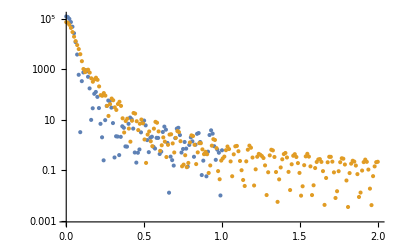

-Graphics-

```mathematica
Short[mycppspeccsv=Import[StringJoin[myspec,"/spectr.txt"],"CSV"],5]
Short[mycppspecanticsv=Import[StringJoin[myspec,"/spectr_anti.txt"],"CSV"],5]

Short[mycppspec=mycppspeccsv[[10;;]],5]
Short[mycppspecanti=mycppspecanticsv[[10;;]],5]

mycppspecPt=(Transpose@mycppspec)[[1]];
mycppspecAntiPt=(Transpose@mycppspec)[[1]];

mycppspecAbs2=(Transpose@mycppspec)[[2]];
mycppspecAntiAbs2=(Transpose@mycppspec)[[2]];

ListLogPlot[{Transpose@{ps,Abs@(Jspec)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
ListLogPlot[{Transpose@{ps,Abs@(JspecAnti)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAntiAbs2}}]
```

```mathematica
T=12.2;
R=8.6;
A=0.1278;

J0Rp[p_]=BesselJ[0,R*p*GeVtoIfm];(*dimensionless*)
J1Rp[p_]=BesselJ[1,R*p*GeVtoIfm];(*dimensionless*)
Y0Tw[p_]=BesselY[0,T*ω[p]*GeVtoIfm];(*dimensionless*)
Y1Tw[p_]=BesselY[1,T*ω[p]*GeVtoIfm];(*dimensionless*)
J0Tw[p_]=BesselJ[0,T*ω[p]*GeVtoIfm];(*dimensionless*)
J1Tw[p_]=BesselJ[1,T*ω[p]*GeVtoIfm];(*dimensionless*)

JT[p_]:=2*Pi*Pi*T*R *fmtoIGeV*fmtoIGeV/p*(
A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])
)*J1Rp[p]
JR[p_]:=2*Pi*Pi*T*R *fmtoIGeV*fmtoIGeV/ω[p]*(
A*p*J1Rp[p]
)*(-Y1Tw[p]+I*J1Tw[p])
```

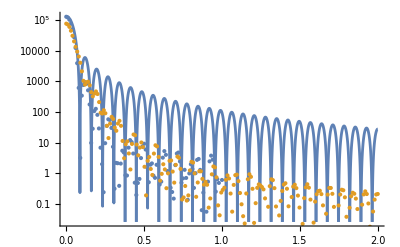

```mathematica
Show[
LogPlot[Abs[JT[p]+JR[p]]^2/(2*Pi)^3,{p,0,2}],
ListLogPlot[{Transpose@{ps,Abs@(Jspec)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
]
```

```mathematica
JT2[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*NIntegrate[rr*fmtoIGeV*fmtoIGeV*BesselJ[0,rr*p*GeVtoIfm],{rr,0,R},Method->{Automatic,"SymbolicProcessing"->0}];
JR2[p_]:=2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*NIntegrate[tt*fmtoIGeV*fmtoIGeV*(-BesselY[0,tt*ω[p]*GeVtoIfm]+I*BesselJ[0,tt*ω[p]*GeVtoIfm]),{tt,0,T},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
sampleps =linspace[0,1,100];
JT2ps=JT2[sampleps];
JR2ps=JR2[sampleps];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) π π ComplexInfinity encountered.

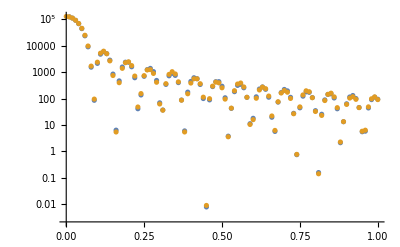

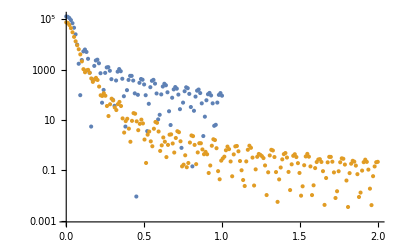

```mathematica
ListLogPlot[{Transpose@{ps,Abs@(JT[ps]+JR[ps])^2/(2*Pi)^3},Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
```

```mathematica
Plot[{r[α],τ[α],Dr[α],Dτ[α]},{α,0,0.60792},PlotLabels->{"r","τ","Dr","Dτ"}]
Plot[{r[α],τ[α],Dr[α],Dτ[α]},{α,0.609,Pi/2},PlotLabels->{"r","τ","Dr","Dτ"}]
```

-Graphics-

-Graphics-

```mathematica
JT3[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*NIntegrate[r[α]*fmtoIGeV*Dr[α]*fmtoIGeV*BesselJ[0,r[α]*p*GeVtoIfm],{α,0,0.60792},Method->{Automatic,"SymbolicProcessing"->0}];
JR3[p_]:=2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*NIntegrate[τ[α]*fmtoIGeV*Dτ[α]*fmtoIGeV*(-BesselY[0,τ[α]*ω[p]*GeVtoIfm]+I*BesselJ[0,τ[α]*ω[p]*GeVtoIfm]),{α,0.61,Pi/2},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
sampleps =linspace[0,1,100];
JT3ps=JT3[sampleps];
JR3ps=JR3[sampleps];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.59742981148369055099944802122990950010716915130615234375}. NIntegrate obtained -0.8169 and 6.37022×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.597429811483691}. NIntegrate obtained 3.80381 and 4.70724×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.523609}. NIntegrate obtained 1.91583 and 2.0717×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 74.0846-113.39 ⅈ and 0.00369177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 76.3588-112.036 ⅈ and 0.00369111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 82.9129-107.711 ⅈ and 0.00368918 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) π π ComplexInfinity encountered.

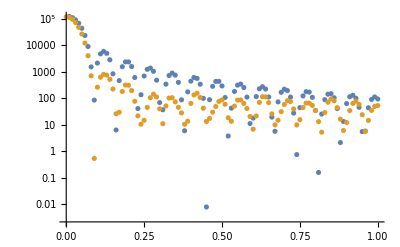

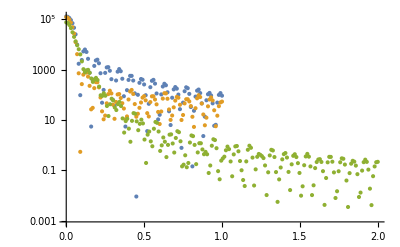

```mathematica
ListLogPlot[{Transpose@{ps,Abs@(JT[ps]+JR[ps])^2/(2*Pi)^3},Transpose@{ps,Abs@(JT3ps+JR3ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3},Transpose@{ps,Abs@(JT3ps+JR3ps)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
```